```mathematica
HW for chapter 2
2012311804 이병호 / 2016314728 정재헌
```

## #1.1

```mathematica
Quit
```

```mathematica
v1={3,7,1}
v2={9,-3,-3}
```

{3,7,1}

{9,-3,-3}

```mathematica
ArcCos[(v1.v2)/(Norm[v1]*Norm[v2])]//N
```

1.53153

```mathematica
180*%/π
```

87.7504

## #1.2

```mathematica
Clear["Global`*"]
```

```mathematica
v={2,3,1}
```

{2,3,1}

```mathematica
dcosa=v[[1]]/Norm[v]
dcosb=v[[2]]/Norm[v]
dcosc=v[[3]]/Norm[v]
```

√(2/7)

3/(√14)

1/(√14)

## #1.3

```mathematica
v1={3,2,1}
v2={1,2,3}
```

{3,2,1}

{1,2,3}

```mathematica
v1.v2
Cross[v1,v2]
```

10

{4,-8,4}

## #1.4

```mathematica
v={a,b,c}
```

{a,b,c}

```mathematica
Norm[v,2]
```

√(Abs[a]^2+Abs[b]^2+Abs[c]^2)

```mathematica
u={1,3,-5}
```

{1,3,-5}

```mathematica
f[x_]:=Norm[u,x]
```

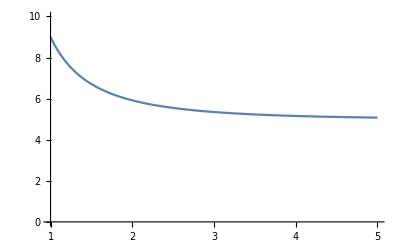

```mathematica
Plot[f[x],{x,1,5},PlotRange->{0,10}]
```

```mathematica
Norm[u,Infinity]
```

5

The result coincides with the fact that -5 has the greatest absolute value, thus Norm[v,infinity]=sup{abs(a),abs(b),abs(c)}

## #1.5

```mathematica
v1={2,0,1}
v2={3,2,1}
v3={a,-2,-1}
```

{2,0,1}

{3,2,1}

{a,-2,-1}

```mathematica
<<"VectorAnalysis`"
```

General::obspkg: VectorAnalysis` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
v4=ScalarTripleProduct[v1,v2,v3]
```

-6-2 a

```mathematica
Solve[v4==0]
```

{{a→-3}}

## #2.1

```mathematica
Clear["Global`*"]
```

```mathematica
A={{1,2,1},{2,-1,0},{1,0,-1}}
```

{{1,2,1},{2,-1,0},{1,0,-1}}

```mathematica
MatrixQ[A]
```

True

### a)

```mathematica
ev=Eigenvalues[A]
```

{-√6,√6,-1}

```mathematica
eiv=Eigenvectors[A]
```

{{1-√6,2,1},{1+√6,2,1},{0,-1,2}}

### b)

```mathematica
p3=Det[A-λ*IdentityMatrix[3]]==0
```

6+6 λ-λ^2-λ^3==0

```mathematica
Solve[p3,λ]
```

{{λ→-1},{λ→-√6},{λ→√6}}

### c)

```mathematica
6*IdentityMatrix[3]+6*A-A.A-A.A.A//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

### d)

```mathematica
eiv[[1]].eiv[[2]]//Simplify
```

0

```mathematica
eiv[[1]].eiv[[3]]//Simplify
```

0

```mathematica
eiv[[2]].eiv[[3]]//Simplify
```

0

## #2-2

```mathematica
Clear["Global`*"]
```

```mathematica
key={{1,2,3,a,1}, {1,4,1,2,3},{2,4,1,2,2},{1,b,2,2,1},{1,2,3,2,2}}//MatrixForm
```

(1 | 2 | 3 | a | 1
1 | 4 | 1 | 2 | 3
2 | 4 | 1 | 2 | 2
1 | b | 2 | 2 | 1
1 | 2 | 3 | 2 | 2)

```mathematica
detkey=Det[key];
```

```mathematica
Det[({{1, 2, 3, a, 1}, {1, 4, 1, 2, 3}, {2, 4, 1, 2, 2}, {1, b, 2, 2, 1}, {1, 2, 3, 2, 2}})]//Simplify
```

12-14 b+3 a (-4+3 b)

```mathematica
Solve[detkey==1,a]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[Det[(1 | 2 | 3 | a | 1
1 | 4 | 1 | 2 | 3
2 | 4 | 1 | 2 | 2
1 | b | 2 | 2 | 1
1 | 2 | 3 | 2 | 2)]==1,a]

```mathematica
Solve[Det[({{1, 2, 3, a, 1}, {1, 4, 1, 2, 3}, {2, 4, 1, 2, 2}, {1, b, 2, 2, 1}, {1, 2, 3, 2, 2}})]==1,a]
```

{{a→(-11+14 b)/(3 (-4+3 b))}}

```mathematica
Solve[Det[({{1, 2, 3, a, 1}, {1, 4, 1, 2, 3}, {2, 4, 1, 2, 2}, {1, b, 2, 2, 1}, {1, 2, 3, 2, 2}})]==1,a]
```

{{a→(-11+14 b)/(3 (-4+3 b))}}

```mathematica
a=a/.%[[1]]
```

(-11+14 b)/(3 (-4+3 b))

```mathematica
Table[%, {b,1,15}]
```

{-1,17/6,31/15,15/8,59/33,73/42,29/17,101/60,5/3,43/26,143/87,157/96,57/35,185/114,199/123}

```mathematica
a/.b->1
```

-1

```mathematica
key=key/.{a->-1,b->1}
```

(1 | 2 | 3 | -1 | 1
1 | 4 | 1 | 2 | 3
2 | 4 | 1 | 2 | 2
1 | 1 | 2 | 2 | 1
1 | 2 | 3 | 2 | 2)

```mathematica
keyinv=Inverse[key]
```

Inverse[(1 | 2 | 3 | -1 | 1
1 | 4 | 1 | 2 | 3
2 | 4 | 1 | 2 | 2
1 | 1 | 2 | 2 | 1
1 | 2 | 3 | 2 | 2)]

```mathematica
Inverse[({{1, 2, 3, -1, 1}, {1, 4, 1, 2, 3}, {2, 4, 1, 2, 2}, {1, 1, 2, 2, 1}, {1, 2, 3, 2, 2}})]
```

{{8,14,-11,30,-29},{-6,-11,9,-23,22},{-2,-4,3,-8,8},{-3,-5,4,-10,10},{8,15,-12,30,-29}}

```mathematica
keyinv={{8,14,-11,30,-29},{-6,-11,9,-23,22},{-2,-4,3,-8,8},{-3,-5,4,-10,10},{8,15,-12,30,-29}}
```

{{8,14,-11,30,-29},{-6,-11,9,-23,22},{-2,-4,3,-8,8},{-3,-5,4,-10,10},{8,15,-12,30,-29}}

```mathematica
Characters["SungKyunKwan University"]
```

{S,u,n,g,K,y,u,n,K,w,a,n, ,U,n,i,v,e,r,s,i,t,y}

```mathematica
CountDistinct[Characters["SungKyunKwan University"]]
```

16

```mathematica
ToCharacterCode["SungKyunKwan University"]
```

{83,117,110,103,75,121,117,110,75,119,97,110,32,85,110,105,118,101,114,115,105,116,121}

```mathematica
plaintext={Take[%,5],Take[%,{6,10}],Take[%,{11,15}],Take[%,{16,20}],Take[%,-5]}//MatrixForm
```

(83 | 117 | 110 | 103 | 75
121 | 117 | 110 | 75 | 119
97 | 110 | 32 | 85 | 110
105 | 118 | 101 | 114 | 115
114 | 115 | 105 | 116 | 121)

```mathematica
cipertext=key.plaintext
```

(1 | 2 | 3 | -1 | 1
1 | 4 | 1 | 2 | 3
2 | 4 | 1 | 2 | 2
1 | 1 | 2 | 2 | 1
1 | 2 | 3 | 2 | 2).(83 | 117 | 110 | 103 | 75
121 | 117 | 110 | 75 | 119
97 | 110 | 32 | 85 | 110
105 | 118 | 101 | 114 | 115
114 | 115 | 105 | 116 | 121)

```mathematica
({{1, 2, 3, -1, 1}, {1, 4, 1, 2, 3}, {2, 4, 1, 2, 2}, {1, 1, 2, 2, 1}, {1, 2, 3, 2, 2}}).({{83, 117, 110, 103, 75}, {121, 117, 110, 75, 119}, {97, 110, 32, 85, 110}, {105, 118, 101, 114, 115}, {114, 115, 105, 116, 121}})
```

{{625,678,430,510,649},{1216,1276,1099,1064,1254},{1185,1278,1104,1051,1208},{722,805,591,692,765},{1054,1147,838,968,1115}}

```mathematica
cipertext={{625,678,430,510,649},{1216,1276,1099,1064,1254},{1185,1278,1104,1051,1208},{722,805,591,692,765},{1054,1147,838,968,1115}}
```

{{625,678,430,510,649},{1216,1276,1099,1064,1254},{1185,1278,1104,1051,1208},{722,805,591,692,765},{1054,1147,838,968,1115}}

```mathematica
keyinv.cipertext
```

{{83,117,110,103,75},{121,117,110,75,119},{97,110,32,85,110},{105,118,101,114,115},{114,115,105,116,121}}

```mathematica
Flatten[%]
```

{83,117,110,103,75,121,117,110,75,119,97,110,32,85,110,105,118,101,114,115,114,115,105,116,121}

```mathematica
FromCharacterCode[%]
```

SungKyunKwan Universrsity